# Definite Integration bug

## Set up the basic functions

You can see the bug directly if you go down to the "here's the bug" heading.

f is the Lorentzian function/Cauchy PDF as defined in Paul Anderson's thesis.  This makes γ the width at half-height, amp the amplitude of the mode, and x0 the location of the mode on the x axis.

```mathematica
f[x_,amp_,γ_,x0_]:=amp γ^2/(4(x-x0)^2+γ^2)
```

d is the negative of the 2nd derivative of a unit height Lorentzian with unit width at half-height with its maximum at 0

```mathematica
d[x_]:=Evaluate[-D[f[x,1,1,0],{x,2}]]
```

Here you can see the formulas for d and the unit f

```mathematica
f[x,1,1,0]
```

1/(1+4 x^2)

```mathematica
d[x]
```

-(128 x^2)/((1+4 x^2)^3)+8/((1+4 x^2)^2)

And here they are, plotted together on the same graph

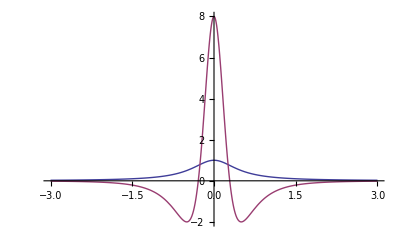

```mathematica
Plot[{f[x,1,1,0],d[x]},{x,-3,3},PlotRange->All]
```

## Is the -2nd derivative a zero-area filter?

Over the whole area, it is zero-area when parameterized acording to the normal parameterization

```mathematica
Integrate[d[x/2], {x, -Infinity, Infinity}]
```

0

However, when parameterized as Paul does, it comes up with a positive area

```mathematica
Integrate[d[x], {x, -Infinity, Infinity}]
```

(3 π)/4

## Here's the bug

I get inconsistent answers for the integral of multiples of the independent area

With a symbol used in the integration, it tells me that the area should be 0 no matter what constant I use

```mathematica
Integrate[d[q x], {x, -Infinity, Infinity},Assumptions->q>0]
```

0

With a constant, it gives me different numbers based on what constant I use for q

```mathematica
Integrate[d[x], {x, -Infinity, Infinity}]
```

(3 π)/4

```mathematica
Integrate[d[(3/4) x], {x, -Infinity, Infinity}]
```

(4 π)/3

```mathematica
Integrate[d[(4/3) x], {x, -Infinity, Infinity}]
```

(63 π)/64

If I directly substitute q into the equation and integrate, I still get inconsistent answers:

```mathematica
d[q x]
```

-(128 q^2 x^2)/((1+4 q^2 x^2)^3)+8/((1+4 q^2 x^2)^2)

```mathematica
Integrate[(-128 q^2 x^2)/((1+4 q^2 x^2)^3)+8/((1+4 q^2 x^2)^2),{x,-Infinity,Infinity},Assumptions->q>0]
```

0

Putting a number in place of q, results are the same as above

```mathematica
Integrate[(-128 1^2 x^2)/((1+4 1^2 x^2)^3)+8/((1+4 1^2 x^2)^2),{x,-Infinity,Infinity}]
```

(3 π)/4

```mathematica
Integrate[(-128 4^2 x^2)/((1+4 4^2 x^2)^3)+8/((1+4 4^2 x^2)^2),{x,-Infinity,Infinity}]
```

(21 π)/64

```mathematica
Integrate[(-128 (9/10)^2 x^2)/((1+4 (9/10)^2 x^2)^3)+8/((1+4 (9/10)^2 x^2)^2),{x,-Infinity,Infinity}]
```

(40 π)/27

```mathematica
Integrate[(-128 (3/4)^2 x^2)/((1+4 (3/4)^2 x^2)^3)+8/((1+4 (3/4)^2 x^2)^2),{x,-Infinity,Infinity}]
```

(4 π)/3